```mathematica
(* Options, definitions etc *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
dx2=Table[2 InverseGammaRegularized[M/2,1-Erf[xσ/Sqrt[2]]]/.M->2//N,{xσ,1,3}]
```

{2.29575,6.18007,11.8292}

```mathematica
Off[Inverse::luc]
```

```mathematica
(* Fiducial model *)
H0=67.27;
h=H0/100;
obh2=0.02225;
och2=0.1198;
mnu=0.06;
mGbeta2 = 1.00;
log10to10As=3.094;
ob=obh2/h^2;
oc=och2/h^2;
ox=1-ob-oc;
w0=-1.;
ns=0.9645;
As=Exp[log10to10As]/10^10;
tau=0.089;
(* cosmo = {Ωb,Ωc,Ωx,Ων,H0,w,ns,As,τ} *)
cosmo={obh2,och2,ns,log10to10As,H0,mnu,mGbeta2};
p={Obh2,Och2,Ns,log10As,H00,Mnu,MGbeta2};
p0={obh2,och2,ns,log10to10As,H0,mnu,mGbeta2};
prs={"ω_b","ω_cdm","n_s","log(10^10A_s)","H_0","m_ν","MG_β2"};
nprms=Length[prs];
combos=Reverse[Table[If[i<j,{i,j}],{i,1,nprms},{j,i,nprms}]][[2;;nprms]][[All,2;;-1]];
Print["fiducial= ",cosmo]
```

fiducial= {0.02225,0.1198,0.9645,3.094,67.27,0.06,1.}

```mathematica
contours[fij_,x_,y_,col_,lims_]:=
With[{X=p[[x]],Y=p[[y]],
dchi2=({p[[x]],p[[y]]}-{p0[[x]],p0[[y]]}).(Inverse[Inverse[fij][[{x,y},{x,y}]]]).({p[[x]],p[[y]]}-{p0[[x]],p0[[y]]})},ContourPlot[{dchi2==dx2[[1]],dchi2==dx2[[2]]},{X,lims[[x,2]],lims[[x,3]]},{Y,lims[[y,2]],lims[[y,3]]},ContourStyle->col]]
joinconts[fm_,num_,i_,lims_]:=Show[Table[contours[fm[k],i[[1]],i[[2]],cols[[k]],lims],{k,1,num}]//Evaluate,Epilog->{Black,Point[p0[[i]]]},FrameLabel->prs[[i]],BaseStyle->FontSize->20]
```

```mathematica
(* end *)
```

```mathematica
FileNames[".//fisher_*.dat"]
```

{./fisher_matrix.dat,./fisher_matrix_lensing.dat,./fisher_matrix_lensing_only_autocorrelations.dat,./fisher_matrix_only_autocorrelations.dat}

```mathematica
FijGC1[1]=Import["./fisher_matrix.dat"];
FijGC1[2]=Import["./fisher_matrix_lensing.dat"];
FijGC1[3]=Import["./fisher_matrix_lensing_only_autocorrelations.dat"];
FijGC1[4]=Import["./fisher_matrix_only_autocorrelations.dat"];
playersGC={"Cross-no-lensing","Cross-lensing","Auto-lensing","Auto-no-lensing"};
numGC=Length[playersGC];
```

```mathematica
FijGC[1]=FijGC1[1][[3;;-1]];
FijGC[2]=FijGC1[2][[3;;-1]];
FijGC[3]=FijGC1[3][[3;;-1]];
FijGC[4]=FijGC1[4][[3;;-1]];
```

```mathematica
bα={-2.7234548600 *10^{-3},-5.3730641064*10^{-02}, 1.3876611210*10^{-01},-6.6152337747*10^{-02}, 1.4026330588*10^{+01}, 1.6461291332*10^{-02}, 3.2831304623*10^{+00}};

Table[
{p[[ii]],bα[[ii]]/p0[[ii]]}
,{ii,1,Length[p]}
]
Table[
{p[[ii]],bα[[ii]]/Sqrt[Inverse[FijGC[2]][[ii,ii]]]}
,{ii,1,Length[p]}
]
```

{{Obh2,{-0.122402}},{Och2,{-0.448503}},{Ns,{0.143874}},{log10As,{-0.0213808}},{H00,{0.208508}},{Mnu,{0.274355}},{MGbeta2,{3.28313}}}

{{Obh2,{-14.7974}},{Och2,{-38.1965}},{Ns,{36.9713}},{log10As,{-11.8307}},{H00,{37.2424}},{Mnu,{3.70107}},{MGbeta2,{45.6284}}}

```mathematica
(* Relative Figures of Merit *)
```

```mathematica
FoMGC=#/Min[#]&/@{Sqrt[Det[FijGC[#]]]&/@Range[1,4]};
Print["Relative FoM for GC: ",playersGC," = ",FoMGC[[1]]]
```

Relative FoM for GC: {Cross-no-lensing,Cross-lensing,Auto-lensing,Auto-no-lensing} = {1.90721,2.75231,1.0254,1.}

```mathematica
limitsGC={{Obh2,0.02165,0.02287},{Och2,0.1147,0.1250},{Ns,0.951,0.976},{log10As,3.074,3.115},{H00,66.1,68.5},{Mnu,0.047,0.073},{MGbeta2,0.7,1.3}};
cols={Black,Blue,Green,Red};
```

```mathematica
(* Marginalized GC contours *)
```

Contours for the GC:

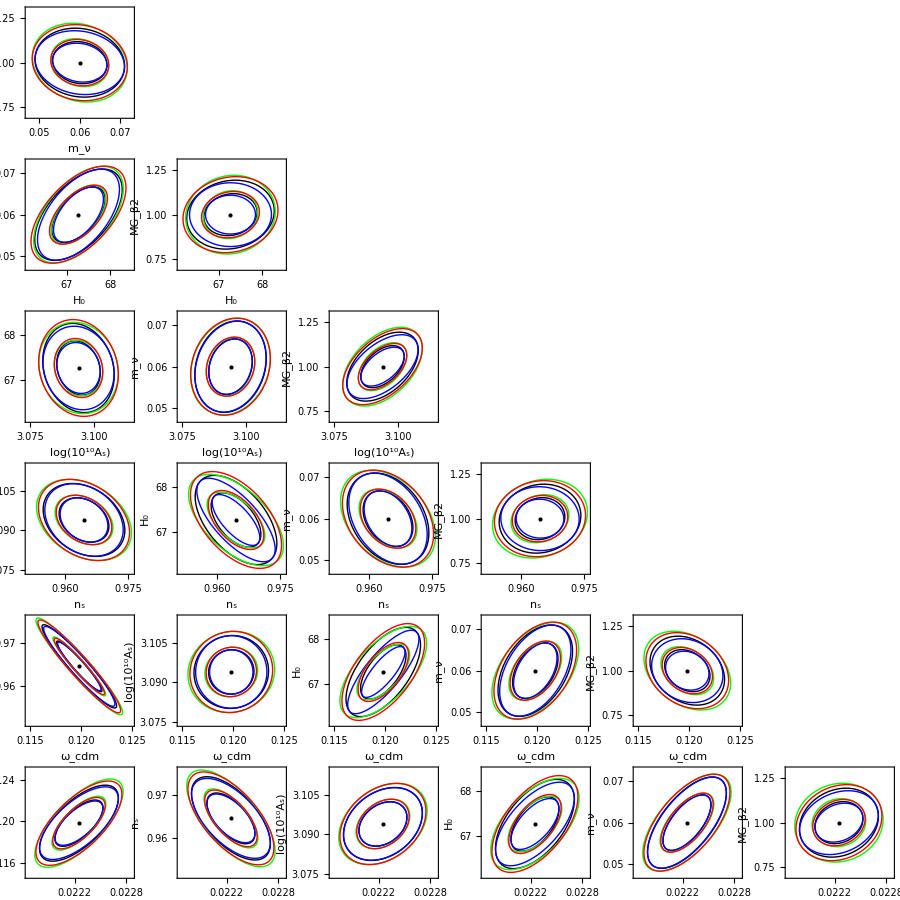

```mathematica
Print[Style[Text["Contours for the GC:"],FontSize->16]];
plotsGC=GraphicsGrid[Table[Table[joinconts[FijGC,numGC,i[[n]],limitsGC],{n,1,Length[i]}],{i,combos}],ImageSize->900,PlotLabel->Table[Style[Text[playersGC[[k]]],{cols[[k]],FontSize->24}],{k,1,numGC}]]
```

```mathematica
Export["contours_GC.pdf",plotsGC,ImageSize->1800]
```

contours_GC.pdf